## libtorch batchsize

Perfect parallelization/vectorization should lead to inference time almost independent of batch size
For the examples run, scaling starts as N^0.25, then transitions to N^1 for larger batch sizes.

Óscar Amaro (Feb 2024)

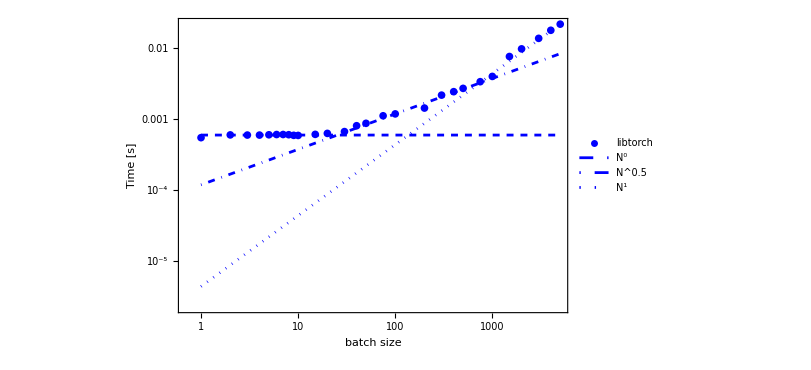

```mathematica
(* set notebook directory *)
SetDirectory[NotebookDirectory[]];

(* load data *)
data=Import["inferenceTime_libtorch_batchsize.csv"];

(* split into columns *)
x=data[[;;,1]];
yNaive=data[[;;,2]];

(* show N scaling *)
y1=x^0;y1=y1*yNaive[[3]]/y1[[3]];
i=Floor[Length[x]/2]+3;
y2=x^0.5;y2=y2*yNaive[[ i]]/y2[[i]];
y3=x^1;y3=y3*yNaive[[-1]]/y3[[-1]];

(* plot*)
ListLogLogPlot[{Transpose[{x,yNaive}],Transpose[{x,y1}],Transpose[{x,y2}],Transpose[{x,y3}]},Joined->{False,True,True,True},PlotLegends->{"libtorch","N^0","N^0.5","N^1"},FrameLabel->{"batch size","Time [s]"},ImageSize->600,Frame->True,PlotStyle->{Blue,{Blue,Dashed},{Blue,DotDashed},{Blue,Dotted}}]
```